Usage example shown below. Feel free to omit all parameters except DatabaseName. Defaults are used for omitted parameters (username/password is root/root, server is localhost and the default port is 8086).

TimeSeries[…]

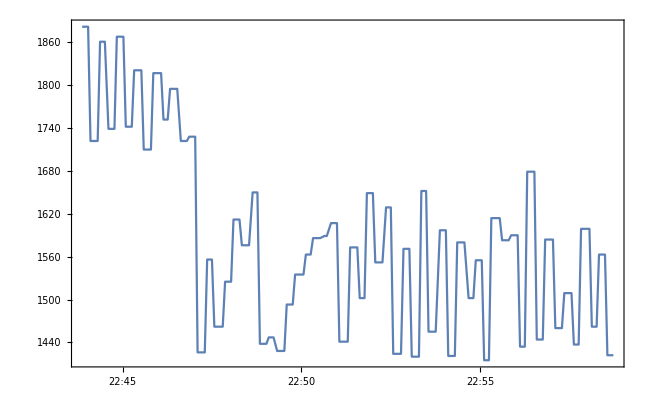

```mathematica
ImportString["SELECT * FROM feed WHERE time > now() - 15m","InfluxDB","ServerName"->"localhost","DatabaseName"->"sensors","UserName"->"root","Password"->"root","ServerPort"->8086]
DateListPlot[%,ImageSize->650]
```